```mathematica
(*Equations A.6 and A.7  n=1*)
Clear[mh,dmh,mw]
mh:=√2
dmh:=0
mw:=mh/2

sol = NDSolve[{a''[r] -(mh^2+dmh^2)*a[r]+(b[r])^2/(4*r)== 0,b''[r]-mw^2*b[r]-(2*b[r])/r^2+mw^2/r*a[r]*b[r]==0,a[0.02]==0.074,a[5.66]==1.13,b[0.02]==0.02,b[5.66]==2.83},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[5.66]==1.13,b[5.66]==2.83,a'[5.66]==-0.3,b'[5.66]==-0.42}}];
```

NDSolve::ndsz: At r == 1.56378, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1.00465, step size is effectively zero; singularity or stiff system suspected.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: There are significant errors {-0.0243215, 0.39045, -0.165789, -0.0613098} in the boundary value residuals.  Returning the best solution found.

```mathematica
Evaluate[a[4.2]/.sol]
```

{2.0503}

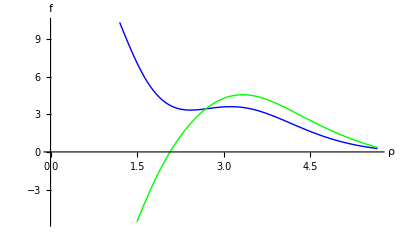

```mathematica
Plot[{Evaluate[a[r] /. sol]/r,Evaluate[b[r] /. sol]/(√2*r)}, {r,0.71,5.66},PlotStyle->{Blue,Green},AxesLabel->{ρ,f},AxesOrigin->{0,0}]
(*a/r is blue   b/r is green*)
```

```mathematica
(*Equations A.6 and A.7*)
Clear[mh,dmh,mw]
mh:=√2
dmh:=0
mw:=mh/2

sol = NDSolve[{c''[r] -(mh^2+dmh^2)*c[r]+(d[r])^2/(4*r)== 0,d''[r]-mw^2*d[r]-(2*d[r])/r^2+mw^2/r*c[r]*d[r]==0,c[1.41]==10.72,c[0.71]==7.89,d[1.41]==-10.01,d[0.71]==-5.89},{c,d},r, Method->{"Shooting","StartingInitialConditions"->{c[1.41]==10.72,d[1.41]==-10.01,c'[1.41]==-0.12,d'[1.41]==-0.08}}];
```

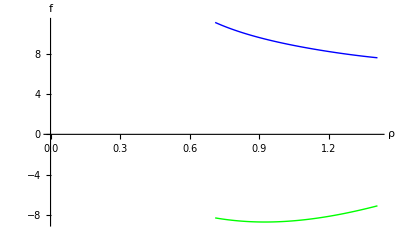

```mathematica
Plot[{Evaluate[c[r] /. sol]/r,Evaluate[d[r] /. sol]/r}, {r,0.71,1.41},PlotStyle->{Blue,Green},AxesLabel->{ρ,f},AxesOrigin->{0,0}]
(*a/r is blue   b/r is green*)
```

```mathematica
Plot[Piecewise[{{Evaluate[c[r] /. sol]/r, {r,0.71,1.41}},{Evaluate[d[r] /. sol]/r, {r,0.71,1.41}},{Evaluate[a[r] /. sol]/r, {r,1.41,7.07}},{Evaluate[b[r] /. sol]/r,{r,1.41,7.07}}}]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[Piecewise[{{Evaluate[c[r]/.sol]/r, {r,0.71,1.41}}, {Evaluate[d[r]/.sol]/r, {r,0.71,1.41}}, {Evaluate[a[r]/.sol]/r, {r,1.41,7.07}}, {Evaluate[b[r]/.sol]/r, {r,1.41,7.07}}}]]

```mathematica
(*Archive

a[7.1]==2.1,a[0.4]==27.8,b[0.4]==-1.6,b[7.1]==6.4},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[7.1]==2.1,b[7.1]==6.4,a'[7.1]==-0.1,b'[7.1]==-0.3}}];*)
```